```mathematica
(*
consulta = "df = pd.read_sql(\"\"\"SELECT patient_id,frace,document_id,token_cancer from Alltokens where document_id 
    between 0 and 1000 and token_cancer in ('CANCER_CONCEPT', 'COMORBIDITY', 'AGE', 'TNM', 'TREATMENT_NAME','DRUG','SURGERY')
    group by document_id,patient_id,frace,token_cancer \"\"\" , con)
    print(df.head(10))
    df.to_csv('alltokens.csv', index=False) ";
*)
```

```mathematica
data=Import["C:\\Users\\brian\\Documents\\00-SEMESTRE-2003-II\\Sistemas complejos\\Proyecto\\alltokens.csv", "Data"];
size = Length[data];
```

Text Normalization

```mathematica
Table[If[StringQ[data[[i,2]]],data[[i,2]]=RemoveDiacritics[ToLowerCase[data[[i,2]]]]],{i,Length[data]}];
```

```mathematica
(*Vista del dataset*)
Table[data[[i,j]],{i,Length[data]},{j,Length[data[[1]]]}] //TableView;
```

```mathematica
RemoveDiacritics["cáncer de mama carcinóma"]
```

cancer de mama carcinoma

Número de registros considerados:

```mathematica
numRegToEval = size-1;
```

ReAjuste de términos sobre dataset para facilitar la visualización del grafo

```mathematica
reglasTokens = {
"AGE"-> "Ag",
"CANCER_CONCEPT" -> "CC",
"COMORBIDITY"-> "Cm",
"DRUG" -> "Dg",
"SURGERY"-> "Sg",
"TNM"-> "TNM",
"TREATMENT_NAME"-> "TN"
};
```

```mathematica
dataFixed = data;
```

```mathematica
dataFixed // TableView;
```

```mathematica
(*Cambio sobre los tokens para su visualizacion*)
dataFixed = dataFixed /. reglasTokens;
(*Cambio registros pacientes - prefijo P*)
Table[dataFixed[[i,1]]= "P:"<>ToString[dataFixed[[i,1]]],{i, 2,numRegToEval}];
(*Cambio registros #doc historia - prefijo H*)
Table[dataFixed[[i,3]]= "H:"<>ToString[dataFixed[[i,3]]],{i, 2,numRegToEval}];
```

```mathematica
EdgeStyling[i_,data_]:= 
Switch[data[[i,4]],
"Ag",Style[data[[i,2]]<-> data[[i,3]],Green],
"CC",Style[data[[i,2]]<-> data[[i,3]],Blue],
"Cm",Style[data[[i,2]]<-> data[[i,3]],Yellow],
"Dg",Style[data[[i,2]]<-> data[[i,3]],Red],
"Sg",Style[data[[i,2]]<-> data[[i,3]],Orange],
"TNM",Style[data[[i,2]]<-> data[[i,3]], Purple],
"TN",Style[data[[i,2]]<-> data[[i,3]], Magenta]];
```

PRUEBA CAMBIO EDGE STYLING  definicion de diccionario con los nodos de cada tipo de token

```mathematica
dicTokens=<|"Ag"->{},"CC"->{},"Cm"->{},"Dg"->{},"Sg"->{},"TNM"->{},"TN"->{}|>;
```

```mathematica
EdgeStyling[i_,data_]:= Module[{},
AppendTo[dicTokens[data[[i,4]]],data[[i,2]]];
Switch[data[[i,4]],
"Ag",Style[data[[i,2]]<-> data[[i,3]],Green],
"CC",Style[data[[i,2]]<-> data[[i,3]],Blue],
"Cm",Style[data[[i,2]]<-> data[[i,3]],Yellow],
"Dg",Style[data[[i,2]]<-> data[[i,3]],Red],
"Sg",Style[data[[i,2]]<-> data[[i,3]],Orange],
"TNM",Style[data[[i,2]]<-> data[[i,3]], Purple],
"TN",Style[data[[i,2]]<-> data[[i,3]], Magenta]]
];
```

```mathematica
nodos = {};
GenerateGraph[data_]:= Module[{doc},
doc = data[[2,3]];
AppendTo[nodos,Labeled[data[[2,1]]<->data[[2,3]],"patient"]];
For[i=2,i<numRegToEval,i++,
AppendTo[nodos,Labeled[EdgeStyling[i,data],data[[i,4]]]];
If[doc != data[[i,3]],AppendTo[nodos,Labeled[data[[i,1]]<->data[[i,3]],"patient"]]; doc=data[[i,3]]];]]

GenerateGraph[dataFixed];
initialGraph = Graph[nodos];
(*SimpleGraph[gp]*)
```

Ajuste de diccionario de nodos en el grafo

```mathematica
dicTokens=AssociationThread[Keys[dicTokens]->Map[DeleteDuplicates,Values[dicTokens]]];
```

Definición del tamaño de los nodos según su grado y arreglo de visualización del grafo

```mathematica
VertexSizes[graph_]:=Module[{sizesVertex={}},
grados=VertexDegree[graph];
vertexs= VertexList[graph];
Table[AppendTo[sizesVertex,If[StringContainsQ[vertexs[[i]],"P:"|"H:"],vertexs[[i]]->1,vertexs[[i]]->1+0.1grados[[i]]]],{i,1,VertexCount[graph]}];
sizesVertex
];
```

```mathematica
shownGraph=Graph[ nodos, VertexLabels->Placed[Automatic,Center], VertexSize->VertexSizes[initialGraph], GraphLayout->"GravityEmbedding"];
```

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[197,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[67,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[88,P:|H:].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

Parte pendiente de revisar ---------

```mathematica
(*Seccion que busca sacar la que sería la lista de nodos particular en una columna, en este caso documentos, con el fin de poderles darles estilo de manera individual*)
documentos = {};
Table[AppendTo[documentos,dataFixed[[i,3]]],{i,2, numRegToEval}];
Table[dataFixed[[i,1]],{i, 2,numRegToEval}];
documentos=DeleteDuplicates[documentos];
```

```mathematica
(*Resaltando nodos de tokens*)
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Ag"],LightGreen]];
shownGraph =HighlightGraph[shownGraph,Style[dicTokens["CC"],LightBlue]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Cm"],LightYellow]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Dg"],LightRed]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Sg"],LightOrange]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TNM"],LightPurple]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TN"],LightMagenta]];
(*shownGraph = HighlightGraph[shownGraph, documentos, GraphHighlightStyle -> "VertexConcaveDiamond"];*)
```

Datos grafo completo

```mathematica
GetInfoGraph[g_]:=Module[{},
Print["Información del Grafo"];
Print["Cantidad de Nodos = ",VertexCount[g]];
Print["Cantidad de Enlaces = ",EdgeCount[g]];
Print["Grado promedio = ", N[Mean[VertexDegree[g]]]]];
```

```mathematica
GetInfoGraph[shownGraph]
```

Información del Grafo

Cantidad de Nodos = 3236

Cantidad de Enlaces = 9047

Grado promedio = 5.59147

GRAFO DE COMUNIDADES -  No se muestra por su dimensión de acuerdo al dataset

```mathematica
CommunityGraphPlot[shownGraph, PlotLegends->Placed[Automatic,Below]];
```

Revisión de comunidades, análisis que busca segmentar grupos de pacientes

```mathematica
comunidades=FindGraphCommunities[shownGraph];
comunidadesPacientes ={};
If[Length[comunidades]>=1,
Table[AppendTo[comunidadesPacientes,Select[comunidades[[i]],StringMatchQ[#,"P:"~~NumberString]&]],{i,1,Length[comunidades]}]
];
comunidadesPacientes;
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[197,P:~~NumberString].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[67,P:~~NumberString].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[58,P:~~NumberString].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

Selección de comunidades que tienen mayor representación sobre todo el dataset para su posterior comparación

```mathematica
comunidadesSeleccionadas={};
Module[{sizeComunidades={},representativiyComty={}},
Table[AppendTo[sizeComunidades,Length[comunidades[[i]]]],{i,1,Length[comunidadesPacientes]}];
totalNodos=Total[sizeComunidades];
(*Calcular respresentatividad por comunidad*)

Table[AppendTo[representativiyComty,sizeComunidades[[i]]/totalNodos],{i,1 ,Length[comunidades]}];
(*Umbral valido para ser aceptado*)
umbralRepresentativity = 0.05;
Table[If[representativiyComty[[i]]>=umbralRepresentativity,AppendTo[comunidadesSeleccionadas,comunidades[[i]]]],{i,1,Length[comunidades]}];
N[representativiyComty];
]
Length[comunidadesSeleccionadas];
```

```mathematica
comunidadesSeleccionadas;
```

Extracción de grafos de cada comunidad seleccionada, previamente seleccionadas de acuerdo al umbral definido

```mathematica
(*Extraccion de subgrafos x comunidad seleccionada, con el fin de extraer los nodos *)
GetGraphsCommunities[globalGraph_,g_]:= Table [Subgraph[globalGraph,g[[i]],Sequence[VertexSize->0.25, GraphLayout->"BipartiteEmbedding"]],{i,Length[g]}];
```

```mathematica
listGraphsValidCommunities=GetGraphsCommunities[shownGraph,comunidadesSeleccionadas];
```

```mathematica
(*Ejemplo de grafo de una comunidad, layout bipartito*)listGraphsValidCommunities[[6]];
```

```mathematica
listGraphsValidCommunities;
```

```mathematica
Table[GetInfoGraph[listGraphsValidCommunities[[i]]],{i,Length[listGraphsValidCommunities]}];
```

Información del Grafo

Cantidad de Nodos = 1003

Cantidad de Enlaces = 2014

Grado promedio = 4.01595

Información del Grafo

Cantidad de Nodos = 532

Cantidad de Enlaces = 1816

Grado promedio = 6.82707

Información del Grafo

Cantidad de Nodos = 393

Cantidad de Enlaces = 683

Grado promedio = 3.47583

Información del Grafo

Cantidad de Nodos = 263

Cantidad de Enlaces = 746

Grado promedio = 5.673

Información del Grafo

Cantidad de Nodos = 226

Cantidad de Enlaces = 468

Grado promedio = 4.14159

Información del Grafo

Cantidad de Nodos = 208

Cantidad de Enlaces = 506

Grado promedio = 4.86538

Eliminación de pacientes de los grafos

```mathematica
(*Eliminación de los pacientes de los grafos bipartitos de una comunidad*)
DeletePacientes[listGraphs_]:=Table[VertexDelete[listGraphs[[i]],
Select[VertexList[listGraphs[[i]]],StringMatchQ[ToString[#],"P:"~~NumberString]&]],{i,Length[listGraphs]}];
```

```mathematica
comunidadesSeleccionadas=DeletePacientes[listGraphsValidCommunities];
```

Extracción de ids de historias clínicas de cada comunidad entre las listas seleccionadas

```mathematica
GetHistoriasClinicas[listGraphs_]:=If[Length[listGraphs]>=1,
Table[Select[VertexList[listGraphs[[i]]],StringMatchQ[ToString[#],"H:"~~NumberString]&],{i,1,Length[listGraphs]}]
];
```

```mathematica
historiasComunidades=GetHistoriasClinicas[comunidadesSeleccionadas];
```

Función que crea una proyección de los nodos de una historia individual, similar a Bipartito entidad-entidad

```mathematica
generateEdges[vertices_List]:=If[Length[vertices]>1,Subsets[vertices,{2}]/. {a_,b_}:>a<->b,{}];
```

```mathematica
project[graph_,vertices_]:=Module[{adjList,edges,g},
adjList=AdjacencyList[graph];
adjList =DeleteCases[Table[If[Length[adjList[[i]]]>1,adjList[[i]]],{i, Length[adjList]}],Null];
(*Print[adjList];*);
edges=DeleteDuplicates[Flatten[Table[generateEdges[adjList[[i]]],{i,Length[adjList]}]]];
(*Print[edges];*);
g=Graph[edges];
VertexDelete[g,vertices]];
```

```mathematica
Length[historiasComunidades[[6]]];
```

```mathematica
projecccionesComunidades=Table[Graph[project[listGraphsValidCommunities[[i]],historiasComunidades[[i]]],PlotTheme->"Scientific"],{i,Length[listGraphsValidCommunities]}];
```

```mathematica
GetInfoGraph[projecccionesComunidades[[1]]]
```

Información del Grafo

Cantidad de Nodos = 871

Cantidad de Enlaces = 12743

Grado promedio = 29.2606

```mathematica
GetInfoGraph[projecccionesComunidades[[6]]]
```

Información del Grafo

Cantidad de Nodos = 142

Cantidad de Enlaces = 1498

Grado promedio = 21.0986

```mathematica
Reverse[Sort[VertexDegree[projecccionesComunidades[[2]]]]];
```

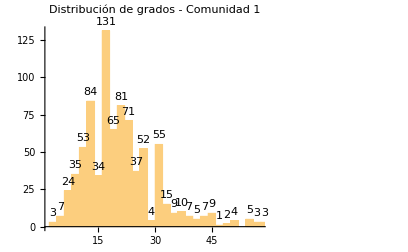

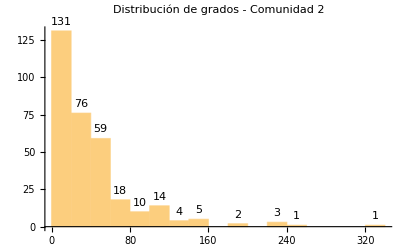

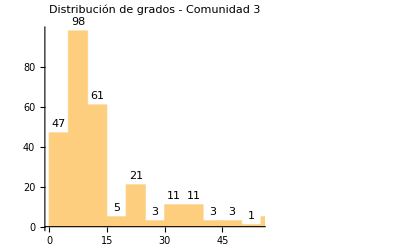

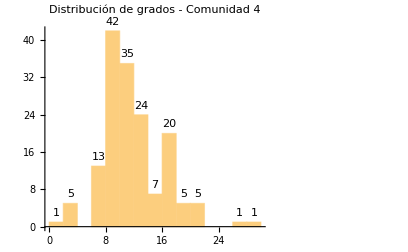

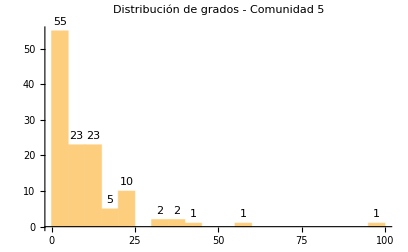

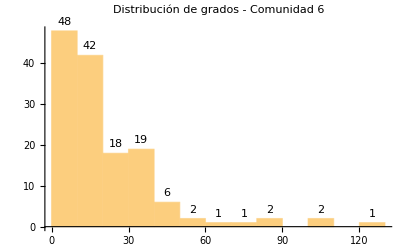

```mathematica
Table[Print[Histogram[VertexDegree[projecccionesComunidades[[i]]],PlotLabel->Style[StringJoin["Distribución de grados - Comunidad ",ToString[i]],"Title",14],LabelingFunction->Above]],{i,Length[projecccionesComunidades]}];
```

Eliminar nodos que se encuentran en gran medida conectados

```mathematica
(*Umbrales que van a servir como filtros dentro de las comunidades*)
umbralGradosComunidades = {160,120,50,24,25,40};
```

```mathematica
(*Eliminación de nodos que no cumplen con los umbrales*)
projecccionesComunidadesReducidas=Table[VertexDelete[projecccionesComunidades[[i]],Select[VertexList[projecccionesComunidades[[i]]],VertexDegree[projecccionesComunidades[[i]],#]<umbralGradosComunidades[[i]]&]],{i,Length[projecccionesComunidades]}];
```

Vista de la información de cada comunidad para ver la reducción

```mathematica
Table[Print[GetInfoGraph[projecccionesComunidadesReducidas[[i]]]],{i,Length[projecccionesComunidadesReducidas]}];
```

Información del Grafo

Cantidad de Nodos = 18

Cantidad de Enlaces = 148

Grado promedio = 16.4444

Null

Información del Grafo

Cantidad de Nodos = 16

Cantidad de Enlaces = 120

Grado promedio = 15.

Null

Información del Grafo

Cantidad de Nodos = 15

Cantidad de Enlaces = 99

Grado promedio = 13.2

Null

Información del Grafo

Cantidad de Nodos = 16

Cantidad de Enlaces = 96

Grado promedio = 12.

Null

Información del Grafo

Cantidad de Nodos = 7

Cantidad de Enlaces = 21

Grado promedio = 6.

Null

Información del Grafo

Cantidad de Nodos = 15

Cantidad de Enlaces = 100

Grado promedio = 13.3333

Null

Extracción de super nodos de cada comunidad para analizar su representación

```mathematica
Table[GraphPlot[projecccionesComunidadesReducidas[[i]]],{i,Length[projecccionesComunidadesReducidas]}];
```

```mathematica
Table[CompleteGraphQ[projecccionesComunidadesReducidas[[i]]],{i,Length[projecccionesComunidadesReducidas]}]
```

{False,True,False,False,True,False}

Con el fin de mejorar la visualización de los grafos, extraemos el nodo de mayor grado de cada comunidad para pasarlo por neighborhoodGraph

```mathematica
nodosMayorGradoPorComunidad=Table[First@MaximalBy[VertexList[projecccionesComunidadesReducidas[[i]]],VertexDegree[projecccionesComunidadesReducidas[[i]],#]&],{i,Length[projecccionesComunidadesReducidas]}]
```

{primario,44 anos,tumor maligno de la mama parte no especificada,dexametasona,mastectomia subtotal,quimioterapia}

```mathematica
Table[Subgraph[projecccionesComunidadesReducidas[[i]],_<->nodosMayorGradoPorComunidad[[i]]],{i,Length[projecccionesComunidadesReducidas]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}